#### Jacobian, Linear terms from the series match with the Jacobian Parameters used {ρ,μ,da, dh}→{0.015,0.24,0.03,5}

```mathematica
eval = Thread[{ρ,μ,da, dh}->{0.015,0.24,0.03,5}]
```

{ρ→0.015,μ→0.24,da→0.03,dh→5}

```mathematica
adot[a_, h_] := ρ+a^2/h-μ a
hdot[a_, h_] := a^2-h
```

```mathematica
sol=Solve[{adot[a,h]==0,hdot[a,h]==0},{a,h}][[1]]
```

{a→(1+ρ)/μ,h→(1+ρ)^2/μ^2}

```mathematica
homfp=Solve[{adot[a0,h0]==0,hdot[a0,h0]==0},{a0,h0}][[1]]
```

{a0→(1+ρ)/μ,h0→(1+ρ)^2/μ^2}

```mathematica
j=D[{adot[a,h],hdot[a,h]},{{a,h}}]/.sol[[1]]
```

{{-μ+(2 (1+ρ))/(h μ),-(1+ρ)^2/(h^2 μ^2)},{(2 (1+ρ))/μ,-1}}

```mathematica
j.{a,h}
```

{-(1+ρ)^2/(h μ^2)+a (-μ+(2 (1+ρ))/(h μ)),-h+(2 a (1+ρ))/μ}

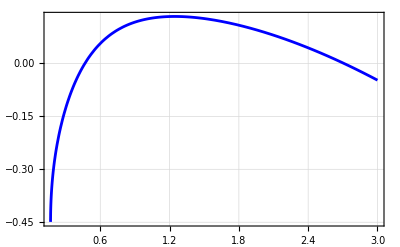

```mathematica
jd=D[{adot[a, h],hdot[a, h]},{{a,h}}]- DiagonalMatrix[{da k^2, dh k^2}];
Plot[Eigenvalues[jd /. sol /. eval][[2]], {k, 0, 3},PlotRange->All,Frame->True,GridLines->Automatic,PlotStyle->Blue]
```

#### Numerical solution for the above parameters

```mathematica
T=100;
δ=1;
```

```mathematica
eqn={1/δ D[a[t,x],{t,1}]==da D[a[t,x],{x,2}]+adot[a[t,x],h[t,x]],1/δ D[h[t,x],{t,1}]==dh D[h[t,x],{x,2}]+hdot[a[t,x],h[t,x]]}/.eval;
ic={a[0,x]==a0+0.01(Cos[x]+10Cos[2x]),h[0,x]==h0+0.01(Cos[x]+10Cos[2x])}/.homfp/.eval;
bc={a[t,-Pi]==a[t,Pi],h[t,-Pi]==h[t,Pi]};
```

```mathematica
{asol,hsol}=NDSolveValue[{eqn,ic,bc},{a,h},{t,0,T},{x,-Pi,Pi},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->400}}];
```

```mathematica
ListAnimate[Table[Plot[{asol[t,x](*,hsol[t,x]*)},{x,-Pi,Pi},PlotRange->{0,15}],{t,0,T,5}]]
```

```mathematica
data=Re[Table[Table[1/Pi NIntegrate[Exp[I k x]asol[t,x],{x,-Pi,Pi},PrecisionGoal->4,AccuracyGoal->5,Method->{Automatic,"SymbolicProcessing"->0}],{t,1,T,5}],{k,1,4}]];
```

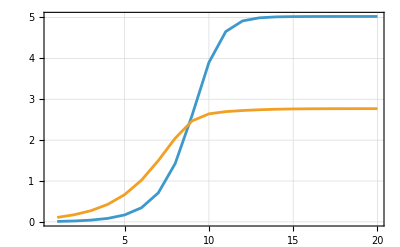

```mathematica
ListLinePlot[data[[;;2]],PlotRange->All,Frame->True,GridLines->Automatic]
```

#### Taylor series for reaction terms

```mathematica
eqs={adot[a+a0,h+h0],hdot[a+a0,h+h0]}(*/.Thread[{a0,h0}->Values[sol]]*)
```

{(a+a0)^2/(h+h0)-(a+a0) μ+ρ,(a+a0)^2-h-h0}

```mathematica
s=Normal[Series[eqs/.Thread[{a,h}->{a t,h t}],{t,0,3}]]
```

{a0^2/h0+((a0^2 h^2-2 a a0 h h0+a^2 h0^2) t^2)/h0^3+((-a0^2 h^3+2 a a0 h^2 h0-a^2 h h0^2) t^3)/h0^4-a0 μ+t ((-a0^2 h+2 a a0 h0)/h0^2-a μ)+ρ,a0^2-h0+(2 a a0-h) t+a^2 t^2}

```mathematica
n2terms=Coefficient[s,t,2]/.h0->a0^2//Simplify
```

{(-a a0+h)^2/a0^4,a^2}

```mathematica
n3terms=Coefficient[s,t,3]/.h0->a0^2//Simplify
```

{-(h (-a a0+h)^2)/a0^6,0}

#### Substituting the eigenvectors Normalization of the eigenvectors - the first component of the right eigenvector is 1 and left eigenvector is normalized to give dot product 1 with the right eigenvector

```mathematica
e[t_]:=Module[{eigvec},
eigvec=Eigensystem[jd/.sol/.eval/.k->t][[2,2]];
Return[eigvec/eigvec[[1]]]]
```

```mathematica
le[t_]:=Module[{leftvec,rightvec},
rightvec=e[t];
leftvec=Eigensystem[Transpose[jd]/.sol/.eval/.k->t][[2,2]];
leftvec=leftvec/(leftvec.rightvec);
Return[leftvec]]
```

```mathematica
subs=Thread[{a,h}->{e[1][[1]](z1 Exp[I x]+Conjugate[z1]Exp[-I x])+e[2][[1]](z2 Exp[2I x]+Conjugate[z2]Exp[-2I x]),e[1][[2]](z1 Exp[I x]+Conjugate[z1]Exp[-I x])+e[2][[2]](z2 Exp[2I x]+Conjugate[z2]Exp[-2I x])}]
```

{a→1. (ⅇ^(ⅈ x) z1+ⅇ^(-ⅈ x) Conjugate[z1])+1. (ⅇ^(2 ⅈ x) z2+ⅇ^(-2 ⅈ x) Conjugate[z2]),h→1.38079 (ⅇ^(ⅈ x) z1+ⅇ^(-ⅈ x) Conjugate[z1])+0.40105 (ⅇ^(2 ⅈ x) z2+ⅇ^(-2 ⅈ x) Conjugate[z2])}

```mathematica
l={Max[Eigenvalues[jd/.sol/.eval/.k->1]]z1,Max[Eigenvalues[jd/.sol/.eval/.k->2]]z2}
```

{0.125706 z1,0.0904837 z2}

```mathematica
q=1/(2Pi){le[1].Integrate[Exp[-I x]n2terms/.subs/.homfp/.eval,{x,-Pi,Pi}],le[2].Integrate[Exp[-2I x]n2terms/.subs/.homfp/.eval,{x,-Pi,Pi}]}//Chop
```

{0.0505528 z2 Conjugate[z1],0.0227347 z1^2}

```mathematica
c=1/(2Pi){le[1].Integrate[Exp[-I x]n3terms/.subs/.homfp/.eval,{x,-Pi,Pi}],le[2].Integrate[Exp[-2I x]n3terms/.subs/.homfp/.eval,{x,-Pi,Pi}]}//Chop
```

{-0.000165565 (35.9298 z1^2 Conjugate[z1]+61.9658 z1 z2 Conjugate[z2]),-0.000163652 (71.3418 z1 z2 Conjugate[z1]+18.8496 z2^2 Conjugate[z2])}

```mathematica
eqsFourier={l,q,c}
```

{{0.125706 z1,0.0904837 z2},{0.0505528 z2 Conjugate[z1],0.0227347 z1^2},{-0.000165565 (35.9298 z1^2 Conjugate[z1]+61.9658 z1 z2 Conjugate[z2]),-0.000163652 (71.3418 z1 z2 Conjugate[z1]+18.8496 z2^2 Conjugate[z2])}}

```mathematica
eqsz1z2=Total[eqsFourier[[All,{1,2}]]]/.{Conjugate[z1]->z1,Conjugate[z2]->z2}//Expand
```

{0.125706 z1-0.00594871 z1^3+0.0505528 z1 z2-0.0102594 z1 z2^2,0.0227347 z1^2+0.0904837 z2-0.0116752 z1^2 z2-0.00308477 z2^3}

```mathematica
solz1z2=NDSolve[Flatten[{(eqsz1z2/.{z1->z1[t],z2->z2[t]})=={z1'[t],z2'[t]},z1[0]==0.01,z2[0]==0.1}],{z1[t],z2[t]},{t,0,200}]
```

{{z1[t]→InterpolatingFunction[…][t],z2[t]→InterpolatingFunction[…][t]}}

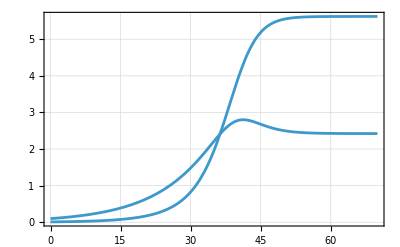

```mathematica
Plot[{z1[t],z2[t]}/.solz1z2,{t,0,70},PlotRange->All,Frame->True,GridLines->Automatic]
```

```mathematica
NSolve[eqsz1z2=={0,0},{z1,z2},Reals]
```

{{z1→5.62115,z2→2.42257},{z1→0.,z2→5.41594},{z1→0.,z2→-5.41594},{z1→-1.78526,z2→-1.59518},{z1→-5.62115,z2→2.42257},{z1→1.78526,z2→-1.59518},{z1→0.,z2→0.}}

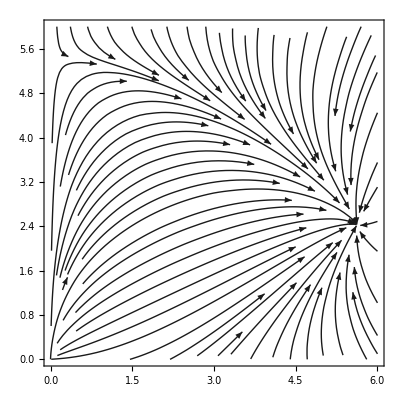

```mathematica
StreamPlot[eqsz1z2,{z1,0,6},{z2,0,6},AspectRatio->True,StreamScale->Full,StreamColorFunction->(GrayLevel[0.1]&),StreamColorFunctionScaling->False]
```

#### Metric + potential Fixed point {z1, z2} = {5.62115, 2.42257}, the fixed point matches with the original equations, only one fixed point has to be matched as origin is implicit and the saddle at {0, z2} is matched simply by keeping beta2 coefficient same

```mathematica
U[z1_,z2_]:=0.5λ1 z1^2+0.5λ2 z2^2-0.25β1 z1^4-0.25β2 z2^4-β z1^2z2^2-γ z1^2z2
eqsz1z2Pot={D[U[z1,z2],z1],D[U[z1,z2],z2]}
```

{-2 z1 z2^2 β-1. z1^3 β1-2 z1 z2 γ+1. z1 λ1,-2 z1^2 z2 β-1. z2^3 β2-z1^2 γ+1. z2 λ2}

```mathematica
param1=Thread[{λ1,λ2,β1,β2}->{0.12570,0.090483,0.005948,0.0030847}]
```

{λ1→0.1257,λ2→0.090483,β1→0.005948,β2→0.0030847}

```mathematica
param2=Solve[Thread[eqsz1z2Pot=={0,0}]/.{z1->5.6211,z2->2.4225}/.param1,{β,γ}]
```

{{β→0.00759343,γ→-0.0312408}}

```mathematica
param=Flatten[Join[param1,param2]]
```

{λ1→0.1257,λ2→0.090483,β1→0.005948,β2→0.0030847,β→0.00759343,γ→-0.0312408}

```mathematica
eqsz1z2
```

{0.125706 z1-0.00594871 z1^3+0.0505528 z1 z2-0.0102594 z1 z2^2,0.0227347 z1^2+0.0904837 z2-0.0116752 z1^2 z2-0.00308477 z2^3}

```mathematica
fpPotential=NSolve[(eqsz1z2Pot=={0,0})/.param,{z1,z2},Reals]
```

{{z1→5.6211,z2→2.4225},{z1→0.,z2→5.41598},{z1→0.,z2→-5.41598},{z1→-1.48918,z2→-1.35465},{z1→-5.6211,z2→2.4225},{z1→1.48918,z2→-1.35465},{z1→0.,z2→0.}}

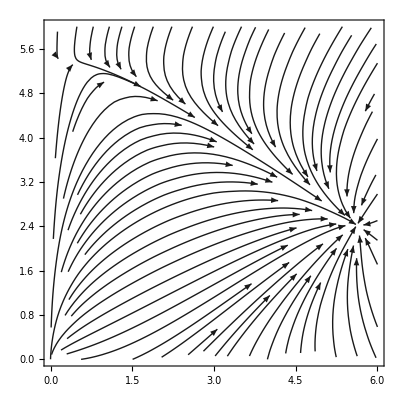

```mathematica
StreamPlot[eqsz1z2Pot/.param,{z1,0,6},{z2,0,6},AspectRatio->True,StreamScale->Full,StreamColorFunction->(GrayLevel[0.1]&),StreamColorFunctionScaling->False]
```

#### Checking the Jacobian and eigenvalues at the stable point

```mathematica
jStable=D[eqsz1z2,{{z1,z2}}]/.fpPotential[[1]]
```

{{-0.375917,0.00475667},{-0.0623783,-0.332725}}

```mathematica
Eigenvalues[jStable]
```

{-0.367347,-0.341295}

```mathematica
jStablePot=D[eqsz1z2Pot,{{z1,z2}}]/.fpPotential[[1]]/.param
```

{{-0.375875,-0.0623869},{-0.0623869,-0.44368}}

```mathematica
Eigenvalues[jStablePot]
```

{-0.480781,-0.338774}

```mathematica
{ν,V}=Eigensystem[jStable];
{σ,Q}=Eigensystem[jStablePot];
```

```mathematica
M=DiagonalMatrix[ν/σ]
```

{{0.764063,0.},{0.,1.00744}}

```mathematica
G=Transpose[Q].M.Q;
Print["G positive definite?: ",PositiveDefiniteMatrixQ[G]];
Print["Eigenvalues match?: ",Sort[Eigenvalues[G.jStablePot]]≈Sort[ν]];
```

G positive definite?: True

Eigenvalues match?: {-0.367347,-0.341295}≈{-0.367347,-0.341295}

```mathematica
Eigenvalues[D[G.eqsz1z2Pot,{{z1,z2}}]/.fpPotential[[1]]/.param]
```

{-0.367347,-0.341295}

#### Metric

```mathematica
a=eqsz1z2;
u=eqsz1z2Pot/.param;
uP={-u[[2]],u[[1]]};
```

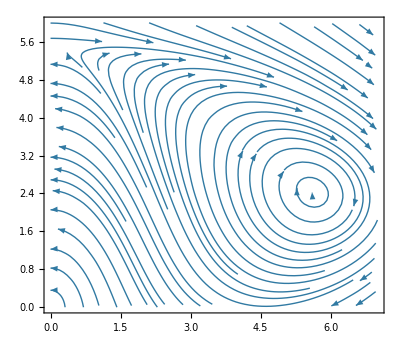

```mathematica
StreamPlot[uP/.param,{z1,0,7},{z2,0,6},StreamColorFunction->None,StreamScale->Full,AspectRatio->True]
```

```mathematica
g=1/(a.u)(Outer[Times, a, Transpose[a]]+Outer[Times,uP,Transpose[uP]]);
```

#### Checking that the metric is positive definite

```mathematica
λMin[x_,y_]:=Min[Eigenvalues[g/.{z1->x,z2->y}]]
```

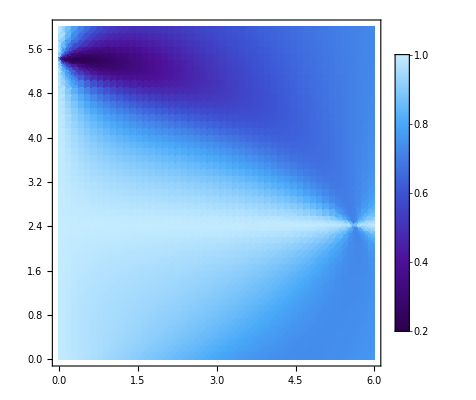

```mathematica
DensityPlot[λMin[x,y],{x,0,6},{y,0,6},ColorFunction->"DeepSeaColors",PlotLegends->BarLegend[Automatic,LabelStyle->12],PlotPoints->50,MaxRecursion->2]
```

#### Solve for a trajectory and checking matching with g.u stream-plot

```mathematica
θ=Table[Pi/2*(1-Exp[-1.5t/2]),{t,0,8,1}]//N;
r=1;
```

```mathematica
spPoints=Table[{r Cos[θ[[i]]],r Sin[θ[[i]]]},{i,Dimensions[θ][[1]]}];
```

```mathematica
gridPoints=Flatten[Table[{x,y},{x,0,6,1},{y,0,6,1}],1];
boundaryPoints=Select[gridPoints,(#[[1]]==0||#[[1]]==6||#[[2]]==0||#[[2]]==6)&];
pts=Join[spPoints,boundaryPoints];
pts=DeleteCases[pts,{0,0}];
```

```mathematica
initialcondition=Table[{z1[0]==pts[[i,1]],z2[0]==pts[[i,2]]},{i,Dimensions[pts][[1]]}];
```

```mathematica
traj=Table[NDSolve[Flatten[{Thread[(a/.{z1->z1[t],z2->z2[t]})=={z1'[t],z2'[t]}],initialcondition[[i]]}],{z1,z2},{t,0,100}],{i,1,Dimensions[pts][[1]]}];
```

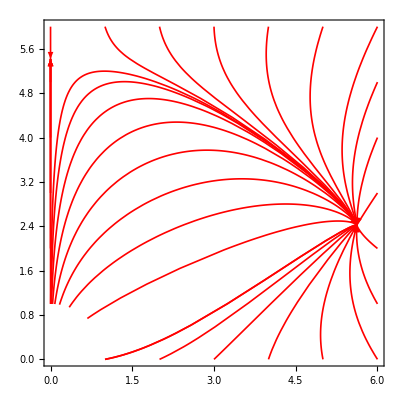

```mathematica
pp=ParametricPlot[Evaluate@Table[{z1[t],z2[t]}/. traj[[i]],{i,Length[pts]}],{t,0,T},PlotStyle->Directive[Red,AbsoluteThickness[1.2]],PlotRange->All,Frame->True,BaseStyle->{FontFamily->"CMU Serif",18}]/. Line[x_]:>{Arrowheads[Table[0.04,{3}]],Arrow[x]}
```

```mathematica
sol=Table[NDSolve[{z1'[t]==(u[[1]]/. {z1->z1[t],z2->z2[t]}),z2'[t]==(u[[2]]/. {z1->z1[t],z2->z2[t]}),z1[0]==p[[1]],z2[0]==p[[2]]},{z1,z2},{t,0,100}],{p,pts}];
```

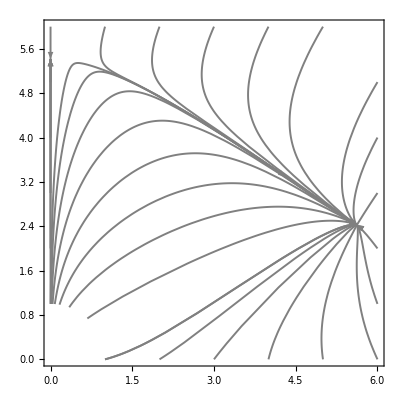

```mathematica
p1new=ParametricPlot[Evaluate@Table[{z1[t],z2[t]}/. sol[[i]],{i,Length[pts]}],{t,0,T},PlotStyle->Directive[Gray,AbsoluteThickness[1.4]],PlotRange->All,Frame->True,BaseStyle->{FontFamily->"CMU Serif",18}]/. Line[x_]:>{Arrowheads[Table[0.04,{3}]],Arrow[x]}
```

```mathematica
uNew=g.u;
```

```mathematica
sol2=Table[NDSolve[{z1'[t]==(uNew[[1]]/. {z1->z1[t],z2->z2[t]}),z2'[t]==(uNew[[2]]/. {z1->z1[t],z2->z2[t]}),z1[0]==p[[1]],z2[0]==p[[2]]},{z1,z2},{t,0,T}],{p,pts}];
```

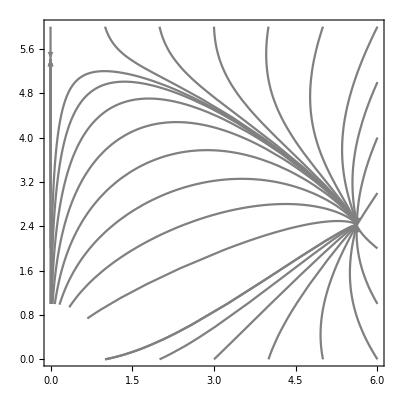

```mathematica
p2new=ParametricPlot[Evaluate@Table[{z1[t],z2[t]}/. sol2[[i]],{i,Length[pts]}],{t,0,T},PlotStyle->Directive[Gray,AbsoluteThickness[1.6]],PlotRange->All,Frame->True,BaseStyle->{FontFamily->"CMU Serif",18}]/. Line[x_]:>{Arrowheads[Table[0.04,{3}]],Arrow[x]}
```

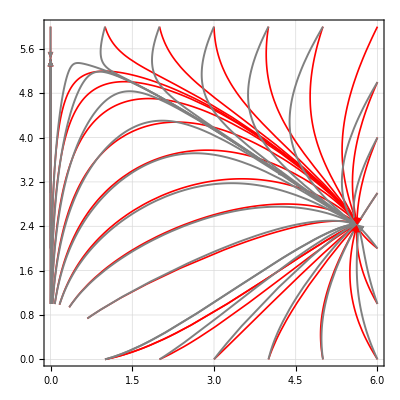

```mathematica
spMetric=Show[pp,p1new,GridLines->Automatic]
```

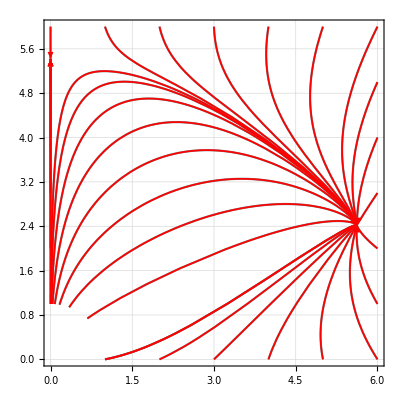

```mathematica
spMetric2=Show[p2new,pp,GridLines->Automatic]
```

#### With just linear metric and potential, this does not match globally as expected

```mathematica
spWithLinearMetric=StreamPlot[G.u,{z1,0,6},{z2,0,6},StreamColorFunction->(GrayLevel[0.1]&),StreamColorFunctionScaling->False,StreamScale->Full];
```

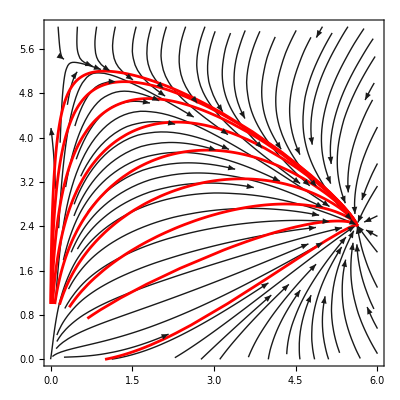

```mathematica
Show[spWithLinearMetric,pp]
```